# Mathematica Demonstration

## Variables

```mathematica
x = 3
y = Pi
z = π
```

3

π

π

Notice a few things:

We can use Greek letters with a certain meaning as variables.

Something like π (and all built-in Mathematica things) needs to be typed with a capital.

The coloring changes when we define a new variable. This can be helpful to see what is defined and what is not.

When you define something, it returns (prints) the same thing we put in. We can suppress this with a semicolon.

```mathematica
x2 = 3;
y2 = Pi;
z2 = π;
sum = x2 + y2 + z2
```

3+2 π

```mathematica
3+2 π
```

3+2 π

```mathematica
(* Notice that the result is not a decimal. It is EXACT: it uses symbols. *)
```

```mathematica
(* To get the previous result, use '%' *)
% / 2
```

1/2 (3+2 π)

```mathematica
(* You can change how it looks, using "Simplify" *)
Simplify[%]
```

3/2+π

```mathematica
(* You can change it back, removing a factor using "Factor" *)
```

```mathematica
Factor[%]
```

1/2 (3+2 π)

```mathematica
(* If we want a decimal, we can ask for it. *)
N[%]
```

4.64159

## Solve algebraic equations

```mathematica
Clear[x, y, z] (* Clear the variables x, y, and z so we can use them again. Notice how the color changes *)
```

```mathematica
Solve[x^2 - 9 == 0, x] (* Notice the double equals *)
```

{{x→-3},{x→3}}

```mathematica
(* Solutions from this are in terms of "rules". Here's an example of a rule. *)
Solve[x^2 - r^2 ==0 , x] (* Solve x^2 - r^2 == 0, which means x = r or x = -r. Then sub r = 3 into the result.  *)
%/.{r->3}
```

{{x→-r},{x→r}}

{{x→-3},{x→3}}

```mathematica
(* This means we can use the result of the solution of x^2 - 9 == 0 in another equation. Let's say we want to know "What is the cube of the solution of the equation x^2 - 9 == 0?" *)
sol = Solve[x^2 - 9==0, x]
x^3/.sol 
(* The variables need to match up. *)
y^3/.sol
```

{{x→-3},{x→3}}

{-27,27}

{y^3,y^3}

```mathematica
(* Mathematica will tell you when it can't solve it. *)
Solve[x^2*Sin[x] + 3 ==0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[3+x^2 Sin[x]==0,x]

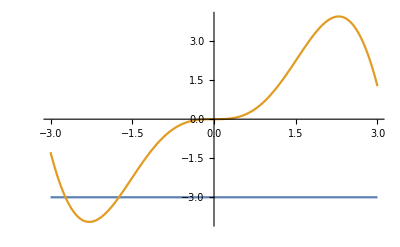

```mathematica
(* This does not mean there is not a solution. We can tell from the plot of x^2*Sin[x] compared to -3 *)
Plot[
{-3, x^2*Sin[x]},{x,-3,3}
] (* The first argument {-3, x^2*Sin[x]} is the things we are plotting. The second argument {x, -3, 3} means "plot for x between -3 and 3." *)
```

```mathematica
(* The solution is at the intersection of the curves. We could solve it numerically. *)
sol = FindRoot[3+x^2*Sin[x]==0,{x,2}] (* Solve 3+x^2*Sin[x]==0 for x near 2 *)
```

{x→-1.74537}

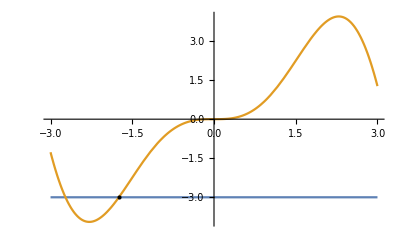

```mathematica
(* If we want to include that on the same plot, we need to use "Show". *)
Show[
Plot[
{-3, x^2*Sin[x]},{x,-3,3}
] (* The first thing we plot*) ,
(* The next thing we plot *)
Graphics[Point[{x, -3}/.sol]]
]
ListPlot[{{x, -3}}/.x->sol]
```

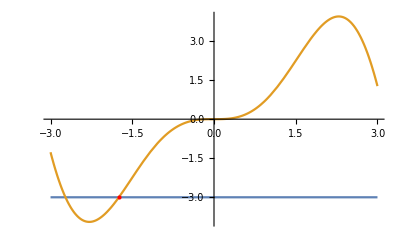

```mathematica
(* Or if we wanted to make that point red and large: *)
Show[
Plot[
{-3, x^2*Sin[x]},{x,-3,3}
] ,
Graphics[{Red, PointSize[Large],Point[{x, -3}/.sol]}]
]
```

## Calculus

```mathematica
D[Sin[x], x] (* Derivative of Sin[x] with respect to x *)
```

Cos[x]

```mathematica
D[x*Tan[x]/(Sin[x]^2 - 3*Exp[x]),x] (* And it can do hard derivatives, no problem. *)
Simplify[%]
```

(x Sec[x]^2)/(-3 ⅇ^x+Sin[x]^2)-(x (-3 ⅇ^x+2 Cos[x] Sin[x]) Tan[x])/((-3 ⅇ^x+Sin[x]^2)^2)+Tan[x]/(-3 ⅇ^x+Sin[x]^2)

(-3 ⅇ^x x Sec[x]^2+Sin[x]^2 (-2 x+Tan[x])+Tan[x] (3 ⅇ^x (-1+x)+x Tan[x]))/((-3 ⅇ^x+Sin[x]^2)^2)

```mathematica
(* It can do integrals. *)
Integrate[
Sec[x],x
]
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]

```mathematica
(* It can even do integrals you probably couldn't, but it does so in terms of "special functions" *)
Integrate[
x*Sec[x],x
]
```

x (Log[1-ⅈ ⅇ^(ⅈ x)]-Log[1+ⅈ ⅇ^(ⅈ x)])+ⅈ (PolyLog[2,-ⅈ ⅇ^(ⅈ x)]-PolyLog[2,ⅈ ⅇ^(ⅈ x)])

```mathematica
(* PolyLog is some special function. *)
```

```mathematica
(* It can also do definite integrals *)
Integrate[
Sec[x],{x,2, Pi}
]
N[%]
```

-2 ArcTanh[Cot[1]]

-1.52345

```mathematica
(* It can also take complicated derivatives of unknown functions. *)
D[f[x]*Tan[g[x]]/(Sin[x]^2 - 3*Exp[x]),x]
```

-(f[x] (-3 ⅇ^x+2 Cos[x] Sin[x]) Tan[g[x]])/((-3 ⅇ^x+Sin[x]^2)^2)+(Tan[g[x]] f'[x])/(-3 ⅇ^x+Sin[x]^2)+(f[x] Sec[g[x]]^2 g'[x])/(-3 ⅇ^x+Sin[x]^2)

```mathematica
(* Notice that it represents f'[x] and g'[x] exactly as that. Let's say we know that both f and g are constants so that f'[x] = 0 and g'[x] = 0. We could then do this *)
Simplify[%/.{f'[x]->0, g'[x]->0}]
```

-(f[x] (-3 ⅇ^x+Sin[2 x]) Tan[g[x]])/((-3 ⅇ^x+Sin[x]^2)^2)

## Differential equations

```mathematica
(* So we can represent derivatives of unknown functions symbolically... this means we can do differential equations! *)
myODE = n'[t] == r*n[t];
sol = DSolve[myODE, n[t],t] (* Again, we get the solution as a replacement rule. *)
```

{{n[t]→ⅇ^(r t) C[1]}}

```mathematica
(* This is actually a list of two rules, you can tell from the double brackets. We can get the first by doing this: *)
sol[[1]]
n[t]/.sol[[1]]
```

{n[t]→ⅇ^(r t) C[1]}

ⅇ^(r t) C[1]

```mathematica
(* This just has some constant Subscript[c, 1]. Let's solve an IVP and define r to get an exact  solution. Make sure to use double equals for equations. *)
```

```mathematica
sol = DSolve[{myODE/.r->3, n[0]==Pi}, n[t],t] (* Again, we get the solution as a replacement rule. *)
```

{{n[t]→ⅇ^(3 t) π}}

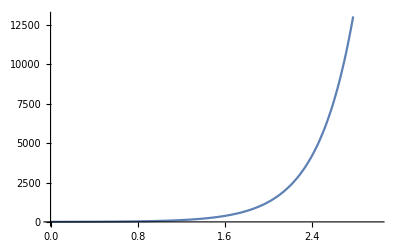

```mathematica
Plot[
n[t]/.sol[[1]],{t,0,3}
]
```

```mathematica
(* This is the same as *)
DSolve[{n'[t]==r*n[t], n[0] ==3 }, n[t],t]
```

{{n[t]→3 ⅇ^(r t)}}

## Eigenvalues

```mathematica
(* Mathematica plays well with linear algebra, but it's a bit clunky. *)
A = {{1, 2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A//MatrixForm (* Doing // after makes it perform the action at the end. It's the same as: *)
MatrixForm[A]
```

(1 | 2
3 | 4)

(1 | 2
3 | 4)

```mathematica
(* For example *)
x(x+2)
x(x+2)//Expand
Expand[x(x+2)]
```

x (2+x)

2 x+x^2

2 x+x^2

```mathematica
Eigensystem[A] (* Gives list of eigenvalues and eigenvectors *)
Eigenvalues[A]
Eigenvectors[A]
```

{{1/2 (5+√33),1/2 (5-√33)},{{1/6 (-3+√33),1},{1/6 (-3-√33),1}}}

{1/2 (5+√33),1/2 (5-√33)}

{{1/6 (-3+√33),1},{1/6 (-3-√33),1}}

## Using Manipulate

```mathematica
(* Manipulate is a very fun and useful tool. It allows you to see how things change when you change a paremeter. Here's some examples from what we saw above. *)
```

```mathematica
Manipulate[
(* All of the things that you want to run go here, ended with semicolons. *)
sol = FindRoot[r+x^2*Sin[x]==0,{x,2}] (* Solve r+x^2*Sin[x]==0 for x near 2 *);
Show[
Plot[
{-r, x^2*Sin[x]},{x,-3,3}
] ,
Graphics[{Red, PointSize[Large],Point[{x, -r}/.sol]}]
]
(* Above is the stuff we want to execute for the variable r, which we have not yet defined. Below defines the range (and hence the slider) we use for r. *)
,
{r, -3, 3} (* This means r can be between -3 and 3, it is a continuous variable. *)
]
```

```mathematica
Manipulate[
sol = DSolve[{n'[t] == r*n[t], n[0]==Pi}, n[t],t] (* Again, we get the solution as a replacement rule. *);
Plot[
n[t]/.sol[[1]],{t,0,3}, PlotRange->{0, 20}
],
{r, -Pi, Pi}
]
```